```mathematica
ClearAll["Global`*"]
```

```mathematica
Off[RowReduce::luc];
```

```mathematica
err=1000;
k=2;
```

## Miscellaneous Functions

```mathematica
η=DiagonalMatrix[{-1,1,1,1}];
```

```mathematica
T={1,0,0,0};
```

```mathematica
CenterT[tet_]:= Total[tet]/Length[tet]
```

```mathematica
To4D[n_]:= Join[{0},n]
To3D[n_]:=Rest[n]
```

```mathematica
distance[V_,i_,j_]:=Block[{ge},ge=DiagonalMatrix[{-1,1,1,1}];(V⟦i⟧-V⟦j⟧).ge.(V⟦i⟧-V⟦j⟧)]
```

```mathematica
AreaTriangle[{x1_,x2_,x3_}]:=Module[{l1,l2,tarea}, l1=x1-x2; l2=x1-x3; tarea=1/2Sqrt[(l1.η.l1)(l2.η.l2) -(l1.η.l2)^2]; Return[tarea]]
```

```mathematica
tetnormal[{x1_,x2_,x3_,x4_},c_]:= Block[{l1,l2,l3,nn,norm},l1=x1-x2; l2=x1-x3;l3=x1-x4; nn=LeviCivitaTensor[4].(η.l1).(η.l2).(η.l3); norm = Sqrt[-nn.η.nn]; If[Refine[nn.(η.(x1-c))>0],Return[nn/norm],Return[-nn/norm]] ]
```

```mathematica
Vertex[vert_,ls3_,ls4_,ls5_]:=Block[{t6,x6,y6,z6,v6,Vertex6},v6={t6,x6,y6,z6};
Vertex6=Join[Vertex5,{v6}];
zz={t6,x6,y6,z6}/.Solve[{distance[Vertex6,1,6]==ls3,If[vert==2,distance[Vertex6,2,6]==ls4,distance[Vertex6,4,6]==ls5],distance[Vertex6,3,6]==ls3,distance[Vertex6,5,6]==ls3},{t6,x6,y6,z6},WorkingPrecision->err]//Quiet;
If[vert==2,Join[Vertex5,{zz⟦2⟧}],Join[Vertex5,{zz⟦1⟧}]]
]
```

```mathematica
Boost[N_,ref_]:=If[N⟦1⟧>0,η+ 1/(1-N.η.ref)(N⊗N+N⊗ref+ref⊗ref)-(1-2N.η.ref)/(1-N.η.ref)(ref⊗N),-(η+ 1/(1+N.η.ref)(N⊗N-N⊗ref+ref⊗ref)-(1+2N.η.ref)/(1+N.η.ref)(-ref⊗N))]
```

```mathematica
ξ[{x_,y_,z_}]:=If[z==-1,{{0},{1}},1/(√2){{√(1+z)},{(x+I*y)/(√(1+z))}}]
```

```mathematica
spinor[ls3_,ls4_,ls5_,n_,m_]:=Block[{gvx},
gvx=gv[n];
Inverse[ConjugateTranspose[gvx]].xi[n,m]/(Inverse[ConjugateTranspose[gvx]].xi[n,m])[[1,1]]]
```

```mathematica
TetNormalsFunc[ls3_,ls4_,ls5_,n_]:=Block[{i,vert,simplexCoord,Vertices0,Vertices,FScenter,tetrahedra,Λ0,vert3,simplexCoord3,FScenter3,RefTetNormalsx},
i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];
Vertices=Vertex[i,ls3,ls4,ls5]//Quiet;
vert=Simplices⟦i⟧;
simplexCoord=Vertices[[#]]&/@vert;
FScenter=FullSimplify@CenterT@simplexCoord;

Λ0=If[i==3,vert3=Simplices⟦3⟧;
simplexCoord3=Vertices[[#]]&/@vert3;
FScenter3=FullSimplify@CenterT@simplexCoord3;tetrahedra[12]=Vertices⟦#⟧&/@Tetrahedra⟦12⟧;RefTetNormalsx=FullSimplify@tetnormal[tetrahedra[12],FScenter3];
-FullSimplify@Boost[RefTetNormalsx,T].η,IdentityMatrix[4]
];

tetrahedra[n]=Vertices⟦#⟧&/@Tetrahedra⟦n⟧;

Λ0.FullSimplify@tetnormal[tetrahedra[n],FScenter]
]
```

```mathematica
kappa[n_,m_,k_]:=Block[{kappa1,kappa2,kappa3,i,output},
i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];

kappa1=Which[(n==11&&m==14)||(n==11&&m==15),1,(n==14&&m==11)||(n==15&&m==11),-1,True,Which[i==1&&n<m,-1,i==2&&n>m,-1,i==3&&n<m,-1,True,1]];

kappa2=Which[(n==11&&m==14)||(n==11&&m==15),1,(n==14&&m==11)||(n==15&&m==11),-1,True,Which[i==1&&n<m,-1,i==2&&n<m,-1,i==3&&n<m,-1,True,1]];

kappa3=Which[(n==11&&m==14)||(n==11&&m==15),-1,(n==14&&m==11)||(n==15&&m==11),1,True,Which[i==1&&n<m,-1,i==2&&n<m,-1,i==3&&n>m,-1,True,1]];

output=Which[k==1,kappa1,k==2,kappa2,k==3,kappa3]
]
```

```mathematica
dihedralAngle[ls3_,ls4_,ls5_,n_,m_]:=Block[{i,vert,Vertices0,Vertices,simplexCoord,FScenter,tetrahedra,TetNormals,sign},
i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];

vert=Simplices⟦i⟧;
Vertices=Vertex[i,ls3,ls4,ls5];
simplexCoord=Vertices[[#]]&/@vert;
FScenter=FullSimplify@CenterT@simplexCoord;

tetrahedra[n]=Vertices⟦#⟧&/@Tetrahedra⟦n⟧;
TetNormals[n]=FullSimplify@tetnormal[tetrahedra[n],FScenter];
tetrahedra[m]=Vertices⟦#⟧&/@Tetrahedra⟦m⟧;
TetNormals[m]=FullSimplify@tetnormal[tetrahedra[m],FScenter];
sign=If[Sign[TetNormals[n]⟦1⟧]==Sign[TetNormals[m]⟦1⟧],-1,1];
sign*Re[ArcCosh[TetNormals[n].η.TetNormals[m]]]
]
```

## Boundary Data for Lorentzian Δ_3 Triangulation

```mathematica
Simplices={{1,2,3,4,5},{1,2,3,5,6},{1,3,4,5,6}};
```

```mathematica
Tetrahedra={{2,3,4,5},{1,2,4,5},{1,2,3,4},{1,3,4,5},{1,2,3,5},{1,2,3,5},{1,2,5,6},{1,3,5,6},{1,2,3,6},{2,3,5,6},{1,3,5,6},{1,3,4,5},{1,4,5,6},{1,3,4,6},{3,4,5,6}};
```

```mathematica
BdFaces=DeleteCases[DeleteDuplicates[Flatten[Subsets[#,{3}]&/@Tetrahedra,1]],{1,3,5}];
```

```mathematica
InternalFaces={{1,3,5}};
```

```mathematica
Triangles=Join[BdFaces,InternalFaces];
```

```mathematica
BDFacesEE={{{1,2}},{{1,3}},{{1,4},{12,15}},{{1,5},{6,10}},{{2,3}},{{2,4},{12,13}},{{2,5},{6,7}},{{3,4},{12,14}},{{3,5},{6,9}},{{7,8},{11,13}},{{7,9}},{{7,10}},{{9,10}},{{13,14}},{{13,15}},{{14,11},{8,9}},{{14,15}},{{15,11},{8,10}}};
```

```mathematica
InternalFacesEE={{{4,5},{6,8},{11,12}}};
```

```mathematica
EE=Join[Flatten[InternalFacesEE,1],Flatten[BDFacesEE,1]];
```

```mathematica
GaugeTetra={4,5,6,8,11,12};
```

```mathematica
ls30=SetPrecision[10.570366003947878,err];
ls40=SetPrecision[29.644435923791924,err];
ls50=SetPrecision[10.519410882819134,err];
```

```mathematica
Vertex5=SetPrecision[{{0,0,0,0},{0,-((2 √10)/3^(3/4)),-((√5)/3^(3/4)),-((√5)/3^(1/4))},{0,0,0,-((2 √5)/3^(1/4))},{-(1/(3^(1/4) √10)),-((√(5/2))/3^(3/4)),-((√5)/3^(3/4)),-((√5)/3^(1/4))},{0,0,-3^(1/4) √5,-((√5)/3^(1/4))}}//N,err];
```

```mathematica
{ls3,ls4,ls5}=Block[{v6},v6=Vertex[2,ls30,ls40,ls50];{distance[v6,1,6],distance[v6,2,6],distance[v6,4,6]}];
```

#### deficit angles

```mathematica
DeficitAngleFlat=dihedralAngle[ls3,ls4,ls5,4,5]+
dihedralAngle[ls3,ls4,ls5,6,8]+
dihedralAngle[ls3,ls4,ls5,11,12]
```

0.

```mathematica
Deficitangles[ls3_,ls4_,ls5_,i_,j_,k_]:=i*dihedralAngle[ls3,ls4,ls5,4,5]+j*dihedralAngle[ls3,ls4,ls5,6,8]+k*dihedralAngle[ls3,ls4,ls5,11,12]
```

### boundary data and critical points

```mathematica
BoundaryData[ls3_,ls4_,ls5_,n_,m_,k_]:=Block[{vert,simplexCoord,i,tetrahedra,Vertices0,Vertices,FScenter,Λ0,vert3,simplexCoord3,FScenter3,TetNormals,triangle,TriangleCoord,Λ,Nab,Arv,nab,xv},
i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];

TetNormals[n]=TetNormalsFunc[ls3,ls4,ls5,n];

TetNormals[m]=TetNormalsFunc[ls3,ls4,ls5,m];

triangle[n,m]=Intersection[Tetrahedra⟦n⟧,Tetrahedra⟦m⟧];

Vertices=Vertex[i,ls3,ls4,ls5];
   
TriangleCoord=Vertices[[#]]&/@triangle[n,m];

Λ=FullSimplify@Boost[TetNormals[n],T];
Arv=AreaTriangle[TriangleCoord];

Nab= (TetNormals[m]+TetNormals[n] (TetNormals[m].η.TetNormals[n] ) )/Sqrt[(TetNormals[m].η.TetNormals[n] ) ^2-1];
nab=kappa[n,m,k]*To3D[Λ.η.Nab];
xv=ξ[nab];
{Arv,nab,kappa[n,m,k],xv}
]
```

#### critical points

```mathematica
g[nab_,θ_]:=Cosh[θ/2]PauliMatrix[0]+Sinh[θ/2]nab.{PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}
```

```mathematica
group[ls3_,ls4_,ls5_,n_]:=Block[{i,ref,nab,theta,g0,g1},
i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];
ref=Which[i==1,5,i==2,6,i==3,12];
g0=Which[ref==5||ref==6,IdentityMatrix[2],ref==12,nab=BoundaryData[ls3,ls4,ls5,5,4,k]⟦2⟧;
theta=dihedralAngle[ls3,ls4,ls5,5,4];g[nab,theta]];
g1=If[n==5||n==6||n==12,g0,nab=BoundaryData[ls3,ls4,ls5,ref,n,k]⟦2⟧;
theta=dihedralAngle[ls3,ls4,ls5,ref,n];g0.g[nab,If[n≤10,theta,If[n>10&&theta>0,theta,-theta]]]];
If[i==1,ConjugateTranspose[Inverse[g1]],g1]
]
```

#### obtain boundary data for each vertex

```mathematica
BDdata1[ls3_,ls4_,ls5_]:=Block[{},
      
Do[xv[EE[[i,1]],EE[[i,2]]]=BoundaryData[ls3,ls4,ls5,EE[[i,1]],EE[[i,2]],k][[4]],{i,Length[EE]}];

Do[xv[EE[[i,2]],EE[[i,1]]]=BoundaryData[ls3,ls4,ls5,EE[[i,2]],EE[[i,1]],k][[4]],{i,Length[EE]}];

Do[nab[EE⟦i,2⟧,EE⟦i,1⟧]=BoundaryData[ls3,ls4,ls5,EE⟦i,2⟧,EE⟦i,1⟧,k]⟦2⟧,{i,Length[EE]}];

Do[nab[EE⟦i,1⟧,EE⟦i,2⟧]=BoundaryData[ls3,ls4,ls5,EE⟦i,1⟧,EE⟦i,2⟧,k]⟦2⟧,{i,Length[EE]}];

Do[Arv[EE⟦i,1⟧,EE⟦i,2⟧]=BoundaryData[ls3,ls4,ls5,EE⟦i,1⟧,EE⟦i,2⟧,k]⟦1⟧,{i,Length[EE]}];

Do[Arv[EE⟦i,2⟧,EE⟦i,1⟧]=BoundaryData[ls3,ls4,ls5,EE⟦i,2⟧,EE⟦i,1⟧,k]⟦1⟧,{i,Length[EE]}];

]
```

#### connect sharing tetrahedra

```mathematica
SO3ToSU2[so3_]:=Block[{el,su2},el=EulerAngles[so3];
su2=Table[WignerD[{1/2,m1,m2},el[[1]],el[[2]],el[[3]]],{m1,-1/2,1/2},{m2,-1/2,1/2}]]
```

```mathematica
hsu2[n_]:=Block[{i,faces,temp,ii,facetemp,so3,xx0,sv,sv0,eqs2,a,xx,su22,su2,sol,eqs},

i=Quotient[n,5,1]+1;
faces=DeleteCases[Table[j,{j,5 i-4,5 i}],n];

temp=If[n==11,8,n];
ii=Quotient[temp,5,1]+1;
facetemp=DeleteCases[Table[j,{j,5 ii-4,5 ii}],temp];

xx0={};
xx={};
sv0={};
sv={};
Table[Table[If[Intersection[Tetrahedra⟦n⟧,Tetrahedra⟦faces⟦i⟧⟧]==Intersection[Tetrahedra⟦temp⟧,Tetrahedra⟦facetemp⟦j⟧⟧],AppendTo[xx,nab[temp,facetemp⟦j⟧]];AppendTo[xx0,nab[n,faces⟦i⟧]];AppendTo[sv,xv[temp,facetemp⟦j⟧]];AppendTo[sv0,xv[n,faces⟦i⟧]],Unevaluated[Sequence[]]],{j,4}],{i,4}];
so3=(RotationMatrix[a,{xx0[[1]],xx[[1]]}]/.Solve[(RotationMatrix[a,{xx0[[1]],xx[[1]]}].xx0[[2]])[[1]]==xx[[2,1]],a,WorkingPrecision->err])//Quiet;

If[Length[so3]==1,su2=SO3ToSU2[so3[[1]]];
eqs=su2.sv0[[-1]]/sv[[-1]]//N//Chop;If[eqs[[1]]==eqs[[2]],su2,"Wrong"],su2=SO3ToSU2[so3[[1]]];
eqs=su2.sv0[[-1]]/sv[[-1]]//N//Chop;su22=SO3ToSU2[so3[[2]]];
eqs2=su22.sv0[[-1]]/sv[[-1]]//N//Chop;Which[eqs[[1]]==eqs[[2]],su2,eqs2[[1]]==eqs2[[2]],su22,True,"Wrong2"]]
]
```

#### Gauge fixed

```mathematica
Sl2cToSu2[{{a_,c_},{b_,d_}}]:=Block[{λ,u,v,mu,upper,su2},λ=Sqrt[Abs[b]^2+Abs[d]^2];u=b/λ;v=d/λ;
mu=a*Conjugate[u]+c*Conjugate[v];
upper={{λ^-1,mu},{0,λ}};
su2={{Conjugate[v],-Conjugate[u]},{u,v}};
{upper,su2}]
```

```mathematica
GaugeGroup[ls3_,ls4_,ls5_,n_]:=Block[{i,temp,gvn0,sl2c,gvn,xvnm,nn,gvnn},

i=If[Mod[n,5]==0,Quotient[n,5],Quotient[n,5]+1];
temp=Which[n==6,5,n==11,8,n==4,12,True,n];
gvn0=group[ls3,ls4,ls5,temp].Inverse[hsu2[temp]];
sl2c=Sl2cToSu2[gvn0];
gvn=sl2c[[1]];

nn=Which[temp==5,6,temp==8,11,temp==12,4];
gvnn=group[ls3,ls4,ls5,nn].Inverse[hsu2[nn]].Inverse[sl2c[[2]]];

{Which[n==5||n==8||n==12,gvn,n==6||n==11||n==4,gvnn],sl2c[[2]]}
]
```

#### obtain boundary data which is fully connected

```mathematica
BDdata2[ls3_,ls4_,ls5_]:=Block[{},

Do[If[MemberQ[GaugeTetra,i],gv[i]=GaugeGroup[ls3,ls4,ls5,i][[1]],gv[i]=group[ls3,ls4,ls5,i].Inverse[hsu2[i]]],{i,1,15}];
      
Do[xi[EE[[i,1]],EE[[i,2]]]=If[MemberQ[GaugeTetra,EE[[i,1]]],GaugeGroup[ls3,ls4,ls5,EE[[i,1]]][[2]].hsu2[EE[[i,1]]].xv[EE[[i,1]],EE[[i,2]]],hsu2[EE[[i,1]]].xv[EE[[i,1]],EE[[i,2]]]],{i,1,Length[EE]}];

Do[xi[EE[[i,2]],EE[[i,1]]]=If[MemberQ[GaugeTetra,EE[[i,2]]],GaugeGroup[ls3,ls4,ls5,EE[[i,2]]][[2]].hsu2[EE[[i,2]]].xv[EE[[i,2]],EE[[i,1]]],hsu2[EE[[i,2]]].xv[EE[[i,2]],EE[[i,1]]]],{i,1,Length[EE]}];

Do[zv[EE⟦i,1⟧,EE⟦i,2⟧]=spinor[ls3,ls4,ls5,EE⟦i,1⟧,EE⟦i,2⟧],{i,1,Length[EE]}]

]
```

### test above functions with non-flat geometry

```mathematica
BDdata1[ls3,ls4,ls5]
```

```mathematica
BDdata2[ls3,ls4,ls5]
```

```mathematica
DeficitAngle=dihedralAngle[ls3,ls4,ls5,4,5]+
dihedralAngle[ls3,ls4,ls5,6,8]+
dihedralAngle[ls3,ls4,ls5,11,12];
```

## Check conditions

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[Inverse[ConjugateTranspose[gv[EE⟦j,1⟧]]].xi[EE⟦j,1⟧,EE⟦j,2⟧]/Inverse[ConjugateTranspose[gv[EE⟦j,2⟧]]].xi[EE⟦j,2⟧,EE⟦j,1⟧],{j,1,30}]]//N
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[gv[EE⟦j,1⟧].xi[EE⟦j,1⟧,EE⟦j,2⟧]/gv[EE⟦j,2⟧].xi[EE⟦j,2⟧,EE⟦j,1⟧],{j,1,30}]]//N
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[If[Length[BDFacesEE[[i]]]==2,ConjugateTranspose[gv[BDFacesEE[[i,1,2]]]].zv[BDFacesEE[[i,1,1]],BDFacesEE[[i,1,2]]]/ConjugateTranspose[gv[BDFacesEE[[i,2,1]]]].zv[BDFacesEE[[i,2,1]],BDFacesEE[[i,2,2]]],Unevaluated[Sequence[]]],{i,Length[BDFacesEE]}]]//N
```

{{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ},{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[ConjugateTranspose[gv[InternalFacesEE[[i,1,2]]]].zv[InternalFacesEE[[i,1,1]],InternalFacesEE[[i,1,2]]]/ConjugateTranspose[gv[InternalFacesEE[[i,2,1]]]].zv[InternalFacesEE[[i,2,1]],InternalFacesEE[[i,2,2]]],{i,Length[InternalFacesEE]}]]//N
```

{{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[ConjugateTranspose[gv[InternalFacesEE[[i,2,2]]]].zv[InternalFacesEE[[i,2,1]],InternalFacesEE[[i,2,2]]]/ConjugateTranspose[gv[InternalFacesEE[[i,3,1]]]].zv[InternalFacesEE[[i,3,1]],InternalFacesEE[[i,3,2]]],{i,Length[InternalFacesEE]}]]//N
```

{{0.+0. ⅈ}}

```mathematica
Map[#⟦1⟧-#⟦2⟧&,Table[ConjugateTranspose[gv[InternalFacesEE[[i,3,2]]]].zv[InternalFacesEE[[i,3,1]],InternalFacesEE[[i,3,2]]]/ConjugateTranspose[gv[InternalFacesEE[[i,1,1]]]].zv[InternalFacesEE[[i,1,1]],InternalFacesEE[[i,1,2]]],{i,Length[InternalFacesEE]}]]//N
```

{{0.+0. ⅈ}}

## EPRL Lorentzian Spinfoam Action

#### define g_a and conjugate g_a

```mathematica
ExpM[z_List]:=Block[{z1,z2,z3,out},If[Length[z]==6,
z1=1+(z⟦1⟧+I z⟦2⟧)/Sqrt[2];z2=(z⟦3⟧+I z⟦4⟧)/Sqrt[2];z3=(z⟦5⟧+I z⟦6⟧)/Sqrt[2];out={{z1,z2},{z3,(1+z2 z3)/z1}},
z1=1+z⟦1⟧/Sqrt[2];z2=(z⟦2⟧+I z⟦3⟧)/Sqrt[2];z3=z3=1/(1+z⟦1⟧/Sqrt[2]);out={{z1,z2},{0,z3}}]
]
```

```mathematica
ExpMconj[z_List]:=Block[{z1,z2,z3,out},If[Length[z]==6,z1=1+(z⟦1⟧-I z⟦2⟧)/Sqrt[2];z2=(z⟦3⟧-I z⟦4⟧)/Sqrt[2];z3=(z⟦5⟧-I z⟦6⟧)/Sqrt[2];out={{z1,z2},{z3,(1+z2 z3)/z1}},
z1=1+z⟦1⟧/Sqrt[2];z2=(z⟦2⟧-I z⟦3⟧)/Sqrt[2];z3=1/(1+z⟦1⟧/Sqrt[2]);out={{z1,z2},{0,z3}}]]
```

```mathematica
LogM[z_]:=Log[z Exp[-I*(1/6*Pi)]]+I*1/6*Pi;
```

#### Define F_(e,x), F_(e,b) and S

```mathematica
Feb1[{e1_,e2_},{zx_,zy_},ge2_List,γ_]:=Block[{gv1e2,zv1bconj,Zv1e2bLeft,Zv1e2bXie2b,gv1e2conj,zv1b,Zv1e2bRight,ZveZve,areas,output},
gv1e2=gv[e2].ExpM[ge2];
zv1bconj={{1},{Conjugate[zv[e1,e2][[2,1]]]+zx-I*zy}};
Zv1e2bLeft=(Transpose[zv1bconj].gv1e2);
Zv1e2bXie2b=Zv1e2bLeft.xi[e2,e1];

gv1e2conj=Transpose[ExpMconj[ge2]].ConjugateTranspose[gv[e2]];
zv1b={{1},{zv[e1,e2][[2,1]]+zx+I*zy}};
Zv1e2bRight=gv1e2conj.zv1b;
ZveZve=Sqrt[Zv1e2bLeft.Zv1e2bRight];

areas=Arv[e1,e2];

output=Flatten[2*areas*LogM[Zv1e2bXie2b/ZveZve]+I *γ*areas*LogM[ZveZve^2]]⟦1⟧
]
```

```mathematica
Feb2[{e3_,e4_},{zx_,zy_},ge3_List,γ_]:=Block[{gv2e3conj,zv2b,Zv1e2bRight,Xie3bZv2e3b,gv2e3,zv2bconj,Zv2e3bLeft,Zv2e3Zv2e3,areas,output},
gv2e3conj=Transpose[ExpMconj[ge3]].ConjugateTranspose[gv[e3]];
zv2b={{1},{zv[e3,e4][[2,1]]+zx+I*zy}};
Zv1e2bRight=gv2e3conj.zv2b;
Xie3bZv2e3b=ConjugateTranspose[xi[e3,e4]].Zv1e2bRight;

gv2e3=gv[e3].ExpM[ge3];
zv2bconj={{1},{Conjugate[zv[e3,e4][[2,1]]]+zx-I*zy}};
Zv2e3bLeft=(Transpose[zv2bconj].gv2e3);
Zv2e3Zv2e3=Sqrt[Zv2e3bLeft.Zv1e2bRight];

areas=Arv[e3,e4];

output=Flatten[2*areas*LogM[Xie3bZv2e3b/Zv2e3Zv2e3]-I *γ*areas*LogM[Zv2e3Zv2e3^2]]⟦1⟧
]
```

```mathematica
Fex[{ve1_,ve2_},{vpe2_,vpe3_},j_,{zx_,zy_},{zpx_,zpy_},gve2_List,gvpe2_List,γ_]:=Block[{gvpeconj,zvp,ZvpxRight,gvpe,zvpconj,ZvpxLeft,gve2x,zvxconj,ZvxLeft,gveconj,zvx,ZvxRight,ZvexZvpex,ZvexZvex,ZvpexZvpex,areas,output},
gvpeconj=Transpose[ExpMconj[gvpe2]].ConjugateTranspose[gv[vpe2]];
zvp={{1},{zv[vpe2,vpe3][[2,1]]+zpx+I*zpy}};
ZvpxRight=gvpeconj.zvp;

gvpe=gv[vpe2].ExpM[gvpe2];
zvpconj={{1},{Conjugate[zv[vpe2,vpe3][[2,1]]]+zpx-I*zpy}};
ZvpxLeft=(Transpose[zvpconj].gvpe);

gve2x=gv[ve2].ExpM[gve2];
zvxconj={{1},{Conjugate[zv[ve1,ve2][[2,1]]]+zx-I*zy}};
ZvxLeft=(Transpose[zvxconj].gve2x);

gveconj=Transpose[ExpMconj[gve2]].ConjugateTranspose[gv[ve2]];
zvx={{1},{zv[ve1,ve2][[2,1]]+zx+I*zy}};
ZvxRight=gveconj.zvx;

ZvexZvpex=ZvxLeft.ZvpxRight;

ZvexZvex=Sqrt[ZvxLeft.ZvxRight];

ZvpexZvpex=Sqrt[ZvpxLeft.ZvpxRight];

areas=Arv[ve1,ve2]+j;

output=Flatten[2*areas*LogM[ZvexZvpex/(ZvexZvex*ZvpexZvpex)]+I *γ*areas*LogM[ZvexZvex^2/ZvpexZvpex^2]]⟦1⟧
]
```

```mathematica
S[varia_List,γ_]:=Block[{gvaria1,gvaria2,gvaria3,gvaria,zvaria,BDfaces,b1,num,num2,num1,DBAmp1,DBAmp2,InterAmp,gvar,xx,yy,pp,bdConnection},
gvaria1=FoldPairList[TakeDrop,varia[[1;;21]],{6,6,6,3}];
gvaria2=FoldPairList[TakeDrop,varia[[22;;42]],{6,6,3,6}];
gvaria3=FoldPairList[TakeDrop,varia[[43;;63]],{6,3,6,6}];
gvaria=Join[gvaria1,gvaria2,gvaria3];

zvaria=Partition[varia[[64;;123]],2];


DBAmp1=Sum[pp=If[Length[BDFacesEE[[a]]]==1,1,2];
num=If[BDFacesEE⟦a,pp,2⟧<10,1,2];gvar=If[BDFacesEE⟦a,pp,2⟧==10||BDFacesEE⟦a,pp,2⟧==15,{0,0,0,0,0,0},gvaria⟦BDFacesEE⟦a,pp,2⟧-num⟧];xx=Position[EE,BDFacesEE⟦a,pp⟧][[1,1]];Feb1[BDFacesEE⟦a,pp⟧,zvaria⟦xx⟧,gvar,γ],{a,Length[BDFacesEE]}];

DBAmp2=Sum[num=If[BDFacesEE⟦a,1,1⟧<10,1,2];gvar=If[BDFacesEE⟦a,1,1⟧==1||BDFacesEE⟦a,1,1⟧==10||BDFacesEE⟦a,1,1⟧==15,{0,0,0,0,0,0},gvaria⟦BDFacesEE⟦a,1,1⟧-num⟧];xx=Position[EE,BDFacesEE⟦a,1⟧][[1,1]];Feb2[BDFacesEE⟦a,1⟧,zvaria⟦xx⟧,gvar,γ],{a,Length[BDFacesEE]}];

bdConnection=Sum[If[Length[BDFacesEE[[a]]]==2,
num1=If[BDFacesEE⟦a,1,2⟧<10,1,2];num2=If[BDFacesEE⟦a,2,1⟧<10,1,2];
xx=Position[EE,BDFacesEE⟦a,1⟧][[1,1]];
yy=Position[EE,BDFacesEE⟦a,2⟧][[1,1]];
Fex[BDFacesEE⟦a,1⟧,BDFacesEE⟦a,2⟧,0,zvaria⟦xx⟧,zvaria⟦yy⟧,gvaria⟦BDFacesEE⟦a,1,2⟧-num1⟧,gvaria⟦BDFacesEE⟦a,2,1⟧-num2⟧,γ],Unevaluated[Sequence[]]],{a,Length[BDFacesEE]}];

InterAmp=Sum[b1=Mod[b+1,3,1];
num1=If[InternalFacesEE⟦a,b,2⟧<10,1,2];num2=If[InternalFacesEE⟦a,b1,1⟧<10,1,2];
xx=Position[EE,InternalFacesEE⟦a,b⟧][[1,1]];
yy=Position[EE,InternalFacesEE⟦a,b1⟧][[1,1]];
Fex[InternalFacesEE⟦a,b⟧,InternalFacesEE⟦a,b1⟧,varia⟦-1⟧,zvaria⟦xx⟧,zvaria⟦yy⟧,gvaria⟦InternalFacesEE⟦a,b,2⟧-num1⟧,gvaria⟦InternalFacesEE⟦a,b1,1⟧-num2⟧,γ],{b,1,3},{a,Length[InternalFacesEE]}];


DBAmp1+DBAmp2+InterAmp+bdConnection
]
```

```mathematica
S[ConstantArray[0,124],γ]//N
```

(0.+45.7123 ⅈ)+(0.+0.219402 ⅈ) γ

```mathematica
DerSym[x_,aa_,γ_]:=Block[{aa1=aa,cmc,pp},aa1[[x]]=cmc;
pp=D[S[aa1,γ],cmc]/.cmc->aa[[x]];If[Precision[pp]<50,Chop[pp,10^-50],pp]]
```

```mathematica
Table[DerSym[i,ConstantArray[0,124],γ],{i,124}]//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
DerSym2[x_,y_,aa_,γ_]:=Block[{aa1=aa,cmc1,cmc2,re,res,pp},If[x==y,{aa1[[x]]=cmc1;
re=D[D[S[aa1,γ],cmc1],cmc1]/.cmc1->aa[[x]]},{aa1[[x]]=cmc1;aa1[[y]]=cmc2;
re=D[D[S[aa1,γ],cmc1],cmc2];}];
pp=re/.{cmc1->aa[[x]],cmc2->aa[[y]]};
If[Precision[pp]<50,Chop[pp,10^-50],pp]]
```

```mathematica
solexpand[n_,γ_]:=Block[{x0,deltax,ϵ,expandToi,eqns0,eqns1,eqns2,sol0,sol},
x0=Table[ToExpression["x"<>ToString[j]],{j,124}];
deltax=ϵ*x0;
expandToi=Series[S[deltax,γ],{ϵ,0,n}];
sol0=ConstantArray[0,124];

For[xx=2,xx≤n,xx++,
eqns0=D[Sum[SeriesCoefficient[expandToi,i],{i,xx}],{x0}];
eqns1=eqns0/.Table[x0[[j]]->sol0[[j]]+ϵ*x0[[j]],{j,124}];
eqns2=Normal[Series[eqns1,{ϵ,0,1}]]/.ϵ->1;
sol=Quiet[Solve[Thread[Flatten[eqns2]==0],x0,WorkingPrecision->err]][[1]];
sol0=sol0+x0/.sol;
];
sol0
]
```

## Solve for complex critical point

```mathematica
CloseKernels[];
LaunchKernels[150];
```

```mathematica
solution[n_,γ_,ls3_,ls4_,ls5_]:=Block[{deficit,DA,Hessianmatrix,sol,oldaction,diff,newaction,correction,DAp,x0,ϵ,deltax,sol0,quadraEqns,quadraEqns1,quadraEqns2,sol1},

sol=solexpand[n,γ];

oldaction=S[ConstantArray[0,124],γ];

newaction=S[sol,γ];

diff=newaction-oldaction;

deficit=Flatten@Table[Deficitangles[ls3,ls4,ls5,a,b,c],{a,{-1,1}},{b,{-1,1}},{c,{-1,1}}];

DAp=Table[DerSym[i,sol,γ],{i,1,124}];

{γ,ls3,ls4,deficit,oldaction,diff,newaction,DAp,sol}]
```

```mathematica
gamma={1/1000000,1/900000,1/800000,1/700000,1/600000,1/500000,1/400000,1/300000,1/200000,1/100000,1/90000,1/80000,1/70000,1/60000,1/50000,1/40000,1/30000,1/20000,1/10000,1/9000,1/8000,1/7000,1/6000,1/5000,1/4000,1/3000,1/2000,1/1000,1/900,1/800,1/700,1/600,1/500,1/400,1/300,1/200,1/100,1/90,1/80,1/70,1/60,1/50,1/40,1/30,1/20,1/10};
```

```mathematica
list5=Array[{}&,Length[gamma]];
SetSharedVariable[list5];

ParallelDo[
lsx=ls4+10^-j;
BDdata1[ls3,lsx,ls5];
BDdata2[ls3,lsx,ls5];

AppendTo[list5[[i]],solution[5,gamma[[i]],ls3,lsx,ls5]],

{i,Length[gamma]},{j,3,15}]//Quiet;
```

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"gammaData.wl"}],list5];
```

```mathematica
list5x={};
SetSharedVariable[list5x];
ParallelDo[
lsx=ls4+10^-j;
BDdata1[ls3,lsx,ls5];
BDdata2[ls3,lsx,ls5];
AppendTo[list5x,solution[5,1/10,ls3,lsx,ls5]],
{j,3,4,1/20}]//Quiet;
```

```mathematica
Save[FileNameJoin[{NotebookDirectory[],"gammaDatax.wl"}],list5x];
```

## Graphs

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"gammaData.wl"}]];
Get[FileNameJoin[{NotebookDirectory[],"gammaDatax.wl"}]];
```

```mathematica
dataerr=Table[{list5[[-1,j,4,1]],Max[Abs[list5[[-1,j,-2]]]]},{j,Length[list5[[-1]]]}];
errs=LinearModelFit[Log[dataerr],{1,x},x]//Normal//N
```

0.170929+5.00002 x

### graph δ_h(r)v.s. δl_26

```mathematica
datatheta=Table[Table[{list5[[-1,i,3]]-ls4,Abs[list5[[-1,i,4,j]]]},{i,2,Length[list5[[-1]]]}],{j,8}];
```

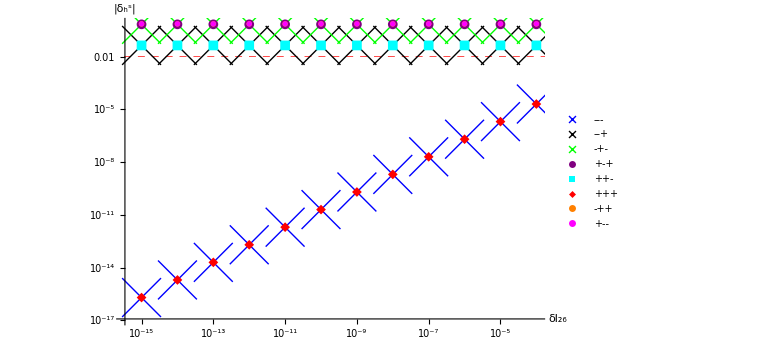

```mathematica
Show[ListLogLogPlot[datatheta[[1;;3]],GridLines->{None,{0.01}},PlotStyle->{Blue,Black,Green},PlotLegends->{"---","--+","-+-"},PlotMarkers->{"×",Offset[40]},GridLinesStyle->Directive[Red,Dashed,Thick]],ListLogLogPlot[datatheta[[6;;8]],PlotStyle->{Purple,Cyan,Red},PlotLegends->{"+-+","++-","+++"},PlotMarkers->{Automatic,Offset[10]}],ListLogLogPlot[datatheta[[4;;5]],PlotStyle->{Orange,Magenta},PlotLegends->{"-++","+--"},PlotMarkers->{"OpenMarkers",Offset[10]},PlotRange->All],AxesLabel->{"δl_26","|δ_h^s|"},AxesStyle->Thick,TicksStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```

### graph δ_h(r)v.s. e^(λ Re[δℐ(r)])

```mathematica
data5x=Table[{list5x[[i,4,-1]],Exp[10^11*Re[list5x[[i,6]]]]},{i,-13,-1}];
```

```mathematica
data1=Join[Table[Abs[{list5[[-1,i,4,-1]],Exp[10^11*Re[list5[[-1,i,6]]]]}],{i,Length[list5[[-1]]]}],Abs[data5x]];
```

```mathematica
data2=Join[Table[{list5[[-1,j,4,-1]],list5[[-1,j,6]]},{j,Length[list5[[-1]]]}],Table[{list5x[[i,4,-1]],list5x[[i,6]]},{i,Length[list5x]}]];fit2=NonlinearModelFit[data2,(a x^2+b x^3+c x^4+d x^5),{a,b,c,d},x];
ff2=Normal[fit2]//N
```

(-0.000158072+0.000828377 ⅈ) x^2-(0.00707542-0.0108233 ⅈ) x^3-(0.0595758+0.0699777 ⅈ) x^4+(0.674299-0.383301 ⅈ) x^5

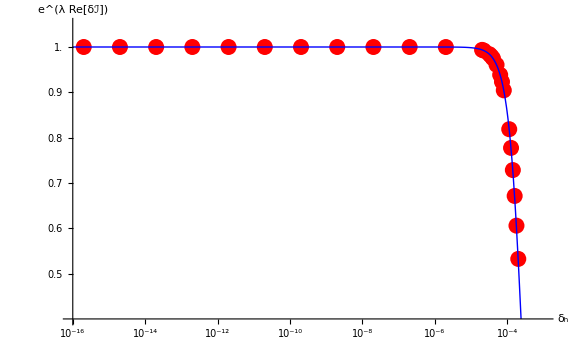

```mathematica
Show[ListPlot[data1,Ticks->{{1.5 10^-12,1.5 10^-8,1.5 10^-4},{1.0,0.9,0.8,0.7,0.6,0.5}},ScalingFunctions->{"Log",None},PlotRange->{{10^-16,10^-3},{0.4,1.05}},PlotStyle->{Red,PointSize[0.02]}],Plot[Exp[10^11*Re[ff2]],{x,10^-16,4.65*10^-1},ScalingFunctions->{"Log",None},PlotStyle->{Blue,Thick},PlotRange->{{10^-16,10^-3},{0.4,1.05}}],AxesLabel->{"δ_h","e^(λ Re[δℐ])"},AxesStyle->Thick,TicksStyle->Thick,ImageSize->Large,LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```

### Contour plot of λ and δ_h(r)

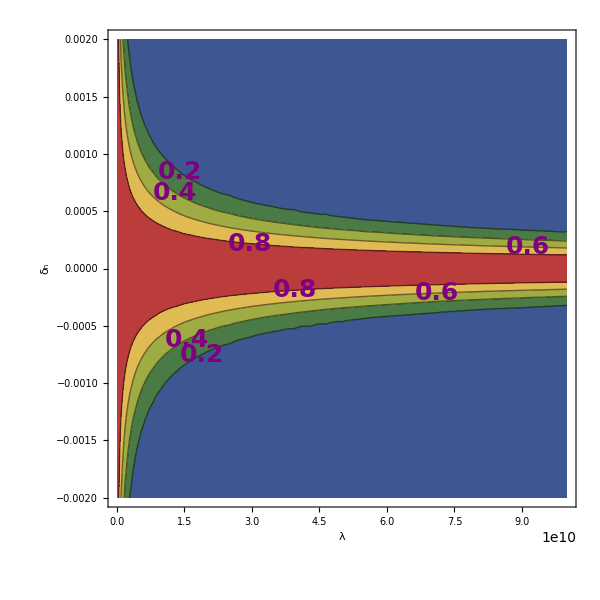

```mathematica
ContourPlot[Exp[λ*ff2],{λ,10,10^11},{x,-2*10^-3,2*10^-3},ContourLabels->(Text[Style[#3,25,Purple,Bold],{#1,#2}]&),Contours->4,ContourStyle->Thick,Mesh->None,ColorFunction->"DarkRainbow",FrameLabel->{"λ","δ_h"},LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```

### Contour plot of λ and γ

```mathematica
gamma={1/1000000,1/900000,1/800000,1/700000,1/600000,1/500000,1/400000,1/300000,1/200000,1/100000,1/90000,1/80000,1/70000,1/60000,1/50000,1/40000,1/30000,1/20000,1/10000,1/9000,1/8000,1/7000,1/6000,1/5000,1/4000,1/3000,1/2000,1/1000,1/900,1/800,1/700,1/600,1/500,1/400,1/300,1/200,1/100,1/90,1/80,1/70,1/60,1/50,1/40,1/30,1/20,1/10};
```

```mathematica
plotfunction=Interpolation[Flatten[Table[{list5[[i,j,1]],list5[[i,j,4,1]],Re[list5[[i,j,6]]]},{i,Length[gamma]},{j,Length[list5[[i]]]}],1]];
```

```mathematica
ContourPlot[Exp[λ*plotfunction[γ,x]]/.λ->5*10^10,{γ,10^-8,10^-1},{x,2*10^-5,10^-3},ContourLabels->(Text[Style[#3,25,Purple,Bold],{#1,#2}]&),Contours->{0.99,0.9,0.8,0.7,0.6,0.5},ContourStyle->Thick,Mesh->None,ColorFunction->"DarkRainbow",FrameLabel->{"γ","δ_h"},LabelStyle->Directive[Black,Bold,25],ImageSize->{600,600}]
```